# Physics through Computational Thinking

## Improved Euler and 4^th order Runge-Kutta Methods

Auditya Sharma and Ambar Jain

Dept. of Physics, IISER Bhopal

Outline

In this lecture we will look at

1. the improved Euler method and how it can dramatically improve over the Euler method.

2. implement Runge-Kutta 4th order method

3. compare various algorithms to solve the ODEs

## Improved Euler’s Method

Improved Euler’s method improves the Euler method by reducing the local error to order h^3 and global error to order h^2.

This is how Improved Euler Method is defined:

t_(n+1)=t_n+h
(x̃)_(n+1)=x_n+h f(t_n,x_n)
x_(n+1)=x_n+h(f(t_n,x_n)+f(t_(n+1), (x̃)_(n+1)))/2

This can also be written as

t_(n+1)=t_n+h
x_(n+1)=x_n+h(f(t_n,x_n)+f(t_n+h, x_n+h f(t_n,x_n)))/2

The improved Euler method is also known as the second-order Runge Kutta (RK) method.

Implementation

```mathematica
eulerImp[F_,X0_,tf_,nMax_]:=Module[{h,datalist,prev,next1,next,rate,rate1},
h=(tf-X0⟦1⟧)/nMax//N;
For[datalist={X0},                                            
Length[datalist]≤nMax,                                             
AppendTo[datalist,next],
prev=Last[datalist];
rate=Through[F@@prev];
next1=prev+h rate;
rate1=Through[F@@next1];
next=prev+h/2(rate+rate1);
];
Return[datalist];
]
```

### Application of Improved Euler to Solve Damped Oscillator

We want to solve the IVP:

ⅆQ/ⅆt=I
ⅆI/ⅆt=-L/(R^2 C)Q-I
Q(0)=1
I(0)=0

Implementation: Lets take the ratio w=L/(R^2 C)

```mathematica
w=10;
beta=√(w-1/4);
(2.0 π)/beta
id[t_,charge_,current_]=1;
chargeDot[t_,charge_,current_]=current;
currentDot[t_,charge_,current_]=-w charge-current;
initial={0,1,0};
```

2.01223

```mathematica
data=eulerImp[{id,chargeDot,currentDot},initial,10,100];
```

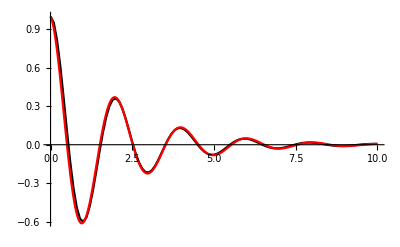

```mathematica
Show[ListPlot[data⟦;;,1;;2⟧,Joined->True,PlotMarkers->None,PlotRange->Full],Plot[ⅇ^(-t/2)Cos[beta t],{t,0,10},PlotRange->Full,PlotStyle->Red]]
```

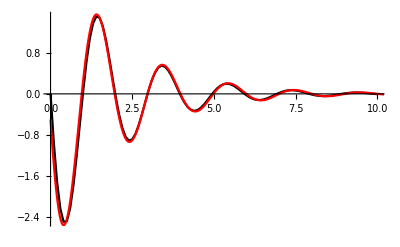

```mathematica
Show[ListPlot[data⟦;;,{1,3}⟧,Joined->True,PlotMarkers->None,PlotRange->Full],Plot[-1/2 ⅇ^(-t/2) Cos[t beta]-ⅇ^(-t/2) beta Sin[t beta],{t,0,20},PlotStyle->Red,PlotRange->Full]]
```

### The Fourth-order Runge-Kutta Method

The fourth-order Runge-Kutta method provides a significant improvement in accuracy, giving a local error of the order h^5, while the global error to order h^4.

When the efficiency increases, the complexity of the method also increases. The RK4 method is often taken to provide an optimum balance between efficiency and complexity.

RK4 method is given by the following prescription:

t_(n+1)=t_n+h
k_1=h f(t_n,x_n)
k_2=h f(t_n+h/2,x_n+1/2 k_1)
k_3=h f(t_n+h/2,x_n+1/2 k_2)
k_4=h f(t_n+h,x_n+k_3)

x_(n+1)=x_n+(k_1+2 k_2+2 k_3+k_4)/6

In order to implement it efficiently we will rephrase the method’s algorithm in terms of rates r_1,r_2 etc. rather than shifts k_1,k_2etc.

t_(n+1)=t_n+h
r_1=k_1/h=f(t_n,x_n)
r_2=k_2/h=f(t_n+h/2,x_n+h/2 r_1)
r_3=k_3/h=f(t_n+h/2,x_n+h/2 r_2)
r_4=k_4/h=f(t_n+h,x_n+h r_3)

x_(n+1)=x_n+h (r_1+2 r_2+2 r_3+r_4)/6

This was for the case of one dynamical quantity. When we have several dynamical quantities, where we expressed set of equations in the matrix form Ẋ=F(X) where X=(t,x,y,z,…)^T.  The RK4 method can be written as

R_1=F(X_n)
R_2=F(X_n+h/2 R_1)
R_3=F(X_n+h/2 R_2)
R_4=F(X_n+h R_3)

X_(n+1)=X_n+h (R_1+2 R_2+2 R_3+R_4)/6

Now the implementation of RK4 method is straightforward:

```mathematica
Clear["Global`*"]
```

```mathematica
rk4[F_,X0_,tf_,nMax_]:=Module[{h,datalist,prev,rate1,rate2,rate3,rate4,next},
h=(tf-X0⟦1⟧)/nMax//N;
For[datalist={X0},                                            
Length[datalist]≤nMax,                                             
AppendTo[datalist,next],
prev=Last[datalist];
rate1=Through[F@@prev];
rate2=Through[F@@(prev+h/2 rate1)];
rate3=Through[F@@(prev+h/2 rate2)];
rate4=Through[F@@(prev+h rate3)];
next=prev+h/6(rate1+2rate2+2rate3+rate4);
];
Return[datalist];
]
```

### Alternative Implementation

In Wolfram Language you can define a function of many arguments in more than one ways:

```mathematica
func[t_,x_]=-x t
func[{t_,x_}]=- x t
```

-t x

-t x

```mathematica
func[1,2]
```

-2

```mathematica
func[{1,2}]
```

-2

We can also define a vector function, that is a function that returns a list of values. For example:

```mathematica
func[{t_,x_}]={x t, x+t, x-t}
```

{t x,t+x,-t+x}

```mathematica
func[{1,2}]
```

{2,3,1}

We can avoided the use of Through function and make a vector definition of  F directly with its argument also being a vector. This is slightly more general in notation and makes function calling a little easier.

We will define rate function F as follows

```mathematica
F[{t_,x_,y_}]:={1, f[t,x,y], g[t,x,y] }
```

where f and g are some function of the arguments. This way we can define the rate function F in one go. Code also appears to be slightly simpler. Here is the implementation

```mathematica
Clear["Global`*"]
```

```mathematica
rk4[F_,X0_,tf_,nMax_]:=Module[{h,datalist,prev,rate1,rate2,rate3,rate4,next},
h=(tf-X0⟦1⟧)/nMax//N;
For[datalist={X0},                                     
Length[datalist]≤nMax,                                             
AppendTo[datalist,next],
prev=Last[datalist];
rate1=F@prev;
rate2=F@(prev+h/2 rate1);
rate3=F@(prev+h/2 rate2);
rate4=F@(prev+h rate3);
next=prev+h/6(rate1+2rate2+2rate3+rate4);
];
Return[datalist];
]
```

This is how we will apply it now:

```mathematica
ω =0.99;
rateFunc[{t_,x_,v_}]={1,v,-x+Cos[ω t]};
initial={0,1,0};
solx[t_]=(-ω^2 Cos[t]+Cos[ω t])/(1-ω^2);
```

```mathematica
w =10;
beta=√(w-1/4);
rateFunc[{t_,x_,v_}]={1,v,-w x-v};
initial={0,1,0};
solx[t_]=ⅇ^(-t/2)Cos[beta t];
```

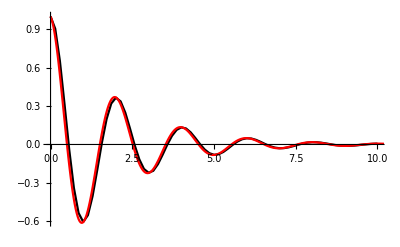

```mathematica
data4=rk4[rateFunc, initial, 10, 70];
Show[ListPlot[data4⟦;;,1;;2⟧,Joined->True,PlotMarkers->None,PlotRange->Full],Plot[solx[t],{t,0,100},PlotRange->Full,PlotStyle->Red]]
```

Now we will implement the Euler Method and RK2 (improved Euler) also in the same way. Then we will compare them for a couple of problems.

```mathematica
euler[F_,X0_,tf_,nMax_]:=Module[{h,datalist,prev},
h=(tf-X0⟦1⟧)/nMax//N;
For[datalist={X0},                                     
Length[datalist]≤nMax,                                             
AppendTo[datalist,prev+h(F@prev)],
prev=Last[datalist];
];
Return[datalist];
]
```

```mathematica
rk2[F_,X0_,tf_,nMax_]:=Module[{h,datalist,prev,rate1,rate2,next},
h=(tf-X0⟦1⟧)/nMax//N;
For[datalist={X0},                                     
Length[datalist]≤nMax,                                             
AppendTo[datalist,next],
prev=Last[datalist];
rate1=F@prev;
rate2=F@(prev+h rate1);
next=prev+h/2(rate1+rate2);
];
Return[datalist];
]
```

### Comparison of various algorithms using Driven Oscillator

Equation of Motion for driven oscillator:     m(ⅆ^2 x)/(ⅆ t^2)=-k x +F cos(ω t).
EOM after non-dimensionalization:            (ⅆ^2 x)/(ⅆ t^2)=-x+cos(ω t)
Equations after reducing EOM to 1st ODEs:  {  ẋ=v
v̇=-x+cos(ω t)
Solution of EOM:    x(t) = -ω^2/(1-ω^2)cos(t)+1/(1-ω^2)cos(ω t)

```mathematica
ω =0.8;
rateFunc[{t_,x_,v_}]={1,v,-x+Cos[ω t]};
initial={0,1,0};
solx[t_]:=(-ω^2 Cos[t]+Cos[ω t])/(1-ω^2);
```

```mathematica
tf=100;
nMax=500;
data1=euler[rateFunc, initial, tf, nMax];
data2=rk2[rateFunc, initial, tf, nMax];
data4=rk4[rateFunc, initial, tf, nMax];
```

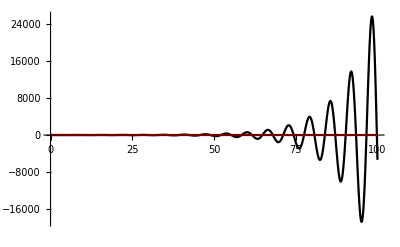
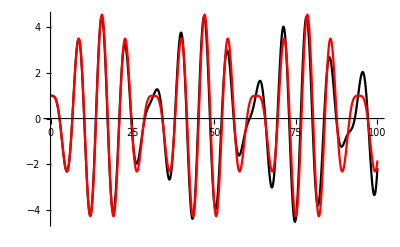
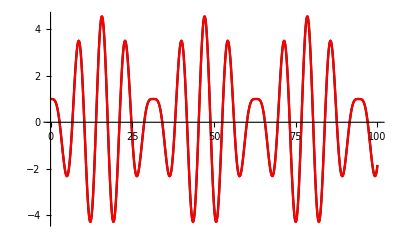

```mathematica
Table[Show[ListPlot[data⟦;;,1;;2⟧,Joined->True,PlotMarkers->None,PlotRange->Full],Plot[solx[t],{t,0,tf},PlotRange->Full,PlotStyle->Red],ImageSize->400],{data,{data1,data2,data4}}]
```

### Error Analysis

We implemented the following err function, a few weeks back, to compute the mean global error, given by equation

err=1/N∑_(i=1)^N |x_i-F(t_i)|

```mathematica
err[dataset_,func_]:=Module[{tlist,xlist,Fxlist},
tlist=dataset⟦;;,1⟧;             (*Extract each time value*)
xlist=dataset⟦;;,2⟧;             (*Extract each x value*)
Fxlist=func/@tlist;                 (*Apply func to each time value to get list of func[Subscript[t, i]]*)
Return[xlist-Fxlist//Abs//Mean];
]
```

### Scaling with h

Lets define the problem

```mathematica
ω =0.2;
rateFunc[{t_,x_,v_}]={1,v,-x+Cos[ω t]};
initial={0,1,0};
solx[t_]:=(-ω^2 Cos[t]+Cos[ω t])/(1-ω^2);
```

Next, we calculate the errors for each of the algorithms and check its scaling with h

Euler Method

```mathematica
tf=20;
Table[dataset=euler[rateFunc, initial, tf, 10^n];
h=tf/10.0^n;
1/h err[dataset⟦;;,1;;2⟧,solx],{n,1,4}]
```

{9.66266,0.296082,0.146228,0.1376}

Improved Euler/Runge Kutta 2nd order

```mathematica
tf=20;
Table[dataset=rk2[rateFunc, initial, tf, 10^n];h=tf/10.0^n;
1/h^2 err[dataset⟦;;,1;;2⟧,solx],{n,1,4}]
```

{2.58767,0.0438949,0.0442324,0.0442784}

Runge Kutta 4th order

```mathematica
tf=20;
Table[dataset=rk4[rateFunc, initial, tf, 10^n];
h=tf/10.0^n;
1/h^4 err[dataset⟦;;,1;;2⟧,solx],{n,1,4}]
```

{0.000918248,0.00216844,0.00219111,0.00362619}

### Comparison for fixed h

Comparison of methods with each other for a fixed value of h:

```mathematica
tf=20;
nMax=1000;
h=(tf-0.0)/nMax
data1=euler[rateFunc, initial, tf, nMax];
data2=rk2[rateFunc, initial, tf, nMax];
data4=rk4[rateFunc, initial, tf, nMax];
{err[data1⟦;;,1;;2⟧,solx],err[data2⟦;;,1;;2⟧,solx],err[data4⟦;;,1;;2⟧,solx]}
```

0.02

{0.00292457,0.000017693,3.50577×10^-10}

### Timing Analysis

Let’s tune n_Max or h so that the errors for each of the methods is approximately comparable:

```mathematica
tf=20;
data1=euler[rateFunc, initial, tf, 30000];
data2=rk2[rateFunc, initial, tf, 2000];
data4=rk4[rateFunc, initial, tf, 100];
{err[data1⟦;;,1;;2⟧,solx],err[data2⟦;;,1;;2⟧,solx],err[data4⟦;;,1;;2⟧,solx]}
```

{0.0000913278,4.42581×10^-6,3.46951×10^-6}

Let’s compare Time taken by each algorithm for solving the problem

```mathematica
euler[rateFunc, initial, 20, 30000];//Timing
```

{2.23345,Null}

```mathematica
rk2[rateFunc, initial, 20, 2000];//Timing
```

{0.034432,Null}

```mathematica
rk4[rateFunc, initial, 20, 100];//Timing
```

{0.002815,Null}

RK4 is the gold standard for solving ODEs when you want to achieve both good accuracy and high efficiency.